```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=
β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[2m],Join[Table[{i,i-1},{i,Range[2,2m,1]}],Table[{i,i+1},{i,Range[1,2m,1]}],Table[{2n-1,2m-2n+2},{n,(m+1)/2}],Table[{2m-2n+2,2n-1},{n,(m-1)/2}]]->-t]
```

```mathematica
T1[t_,m_]:=T1[t,m]=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2m-2n+1},{n,(m-1)/2}]->t]
```

```mathematica
ρ[t_,m_]:=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2n},{n,(m-1)/2}]->t]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_,m_]:=LEFT[ω,δ,t,ϵ,m]=Module[{J=Inverse[β[ω,δ,t,ϵ,m]],B:=Inverse[β[ω,δ,t,ϵ,m]],T1:=T1[1,m]},Do[J=Inverse[IdentityMatrix[2m]-B.ConjugateTranspose[T1].J.T1].B,8000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_,m_]:= Inverse[β[ω,δ,t,ϵ,m]]
SR[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m]=Inverse[IdentityMatrix[2m]-g[ω,δ,t,ϵ,m].ConjugateTranspose[T1[t,m]].LEFT[ω,δ,t,ϵ,m].T1[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,ϵ1_,m_]:=Module[{},η=Module[{gg=g[ω,δ,t,ϵ,m],T=T1[1,m]},
sl1= Module[{J=SR[ω,δ,t,ϵ,m]},Do[J=Module[{c=RandomChoice[{Inverse[Module[{i=β[ω,δ,t,ϵ,m],μ1=RandomInteger[{1,2m}]},ReplacePart[i,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[2m]-c.ConjugateTranspose[T].J.T].c],4]; J=J]; Il1:=Inverse[IdentityMatrix[2m]-sl1.ρ[1,m].SR[ω,δ,t,ϵ,m].ρ[1,m]].sl1;Ir1:=Inverse[IdentityMatrix[2m]-SR[ω,δ,1,0,m].ρ[1,m].sl1.ρ[1,m]].SR[ω,δ,1,0,m];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,1,0,m].ρ[1,m].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.ρ[1,m].grr1.ρ[1,m]-ρ[1,m].GNON1.ρ[1,m].GNON1]]];
η]
```

```mathematica
tr[1,0.0001,1,0,0,7]
```

2.99293

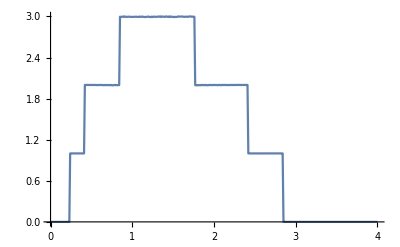

```mathematica
ListLinePlot[Table[{ω,tr[ω,0.0001,1,0,0,7]},{ω,Range[0,4,0.01]}]]
```

```mathematica
imp1[ω_,δ_,t_,ϵ_,ϵ1_,m_]:=Inverse[β[ω,δ,t,ϵ,m]-Module[{κ=β[0,0,0,0,m],i=RandomInteger[{1,14}]},ReplacePart[κ,{{i,i}}->ϵ1]]]
```

```mathematica
imp2[ω_,δ_,t_,ϵ_,ϵ1_,m_]:=Inverse[β[ω,δ,t,ϵ,m]-Module[{κ=β[0,0,0,0,m],i=RandomInteger[{1,7}],j=RandomInteger[{8,14}]},ReplacePart[κ,{{i,i},{j,j}}->ϵ1]]]
```

```mathematica
imp[ω_,δ_,t_,ϵ_,ϵ1_,m_]:=Inverse[β[ω,δ,t,ϵ,m]-Module[{κ=β[0,0,0,0,m],i=RandomInteger[{1,7}],j=RandomInteger[{8,14}]},ReplacePart[κ,{{i,i},{j,j}}->0]]]
```

```mathematica
set[ω_,δ_,t_,ϵ_,ϵ1_,m_,x_,y_,z_]:=RandomSample[Join[Table[imp1[ω,δ,t,ϵ,ϵ1,m],x],Table[imp2[ω,δ,t,ϵ,ϵ1,m],y],Table[imp[ω,δ,t,ϵ,0,m],z]]]
```

```mathematica
set[0,0.0001,0,0,0,7,14,0,86]
```

```mathematica
imp[ω_,δ_,t_,ϵ_,ϵ1_,m_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m],μ=RandomInteger[{1,14}]},ReplacePart[κ,{{μ,μ}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
tr14[ω_,δ_,t_,ϵ_,ϵ1_,m_,numimp_]:=
Module[{x=T1[t,m],T=ρ[t,m]},
list={set[ω,δ,t,ϵ,ϵ1,m,numimp,0,100-numimp]};sl1= Module[{J=SL[ω,δ,t,ϵ,m]},Do[J=Inverse[IdentityMatrix[14]-list[[1,ζ]].ConjugateTranspose[x].J.x].list[[1,ζ]],{ζ,1,100}]; J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,δ,t,ϵ,m].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ,m].T.sl1.T].SR[ω,δ,t,ϵ,m];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,t,ϵ,m].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>3,3,Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]]
```

```mathematica
Mean[Table[tr14[1,0.0001,1,0,0.5,7,14],2000]]
```

2.38756

```mathematica
Mean[Table[tr14[1,0.0001,1,0,0.5,7,14],2000]]
```

2.38729

```mathematica
Export["14imp100.csv",Table[{ω,Mean[Table[tr14[ω,0.0001,1,0,0.5,7,14],2000]]},{ω,Range[0,4,0.01]}]]
```

14imp100.csv

```mathematica
Export["28imp100.csv",Table[{ω,Mean[Table[tr14[ω,0.0001,1,0,0.5,7,28],2000]]},{ω,Range[0,4,0.01]}]]
```

28imp100.csv

```mathematica
Export["42imp100.csv",Table[{ω,Mean[Table[tr14[ω,0.0001,1,0,0.5,7,42],2000]]},{ω,Range[0,4,0.01]}]]
```

42imp100.csv

```mathematica
Export["56imp100.csv",Table[{ω,Mean[Table[tr14[ω,0.0001,1,0,0.5,7,56],2000]]},{ω,Range[0,4,0.01]}]]
```

56imp100.csv

```mathematica
Export["70imp100.csv",Table[{ω,Mean[Table[tr14[ω,0.0001,1,0,0.5,7,70],2000]]},{ω,Range[0,4,0.01]}]]
```

70imp100.csv

```mathematica
Export["84imp100.csv",Table[{ω,Mean[Table[tr14[ω,0.0001,1,0,0.5,7,84],2000]]},{ω,Range[0,4,0.01]}]]
```

84imp100.csv

```mathematica
StringLength["84imp100.csv"]
```

12

```mathematica
misfit[ϵ1_,x_,y_]:=Module[{Tin=T1[1,7],T=ρ[1,7]},
tra:=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{1,1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{2,2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{3,3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{4,4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{5,5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{6,6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{7,7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{8,8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{9,9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{11,11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{12,12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{13,13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp11,imp12,imp1,imp11,imp6,imp12,imp2,imp1,imp5,imp6,imp10,imp13,imp6,imp2,imp4,imp13,imp13,imp8,imp9,imp3,imp8,imp9,imp1,imp5,imp9,imp7,imp1,imp12,imp4,imp3,imp3,imp3,imp5,imp1,imp9,imp4,imp14,imp7,imp3,imp12,imp14,imp1,imp2,imp1,imp11,imp2,imp12,imp3,imp2,imp14,imp12,imp6,imp7,imp7,imp12,imp10,imp1,imp2,imp8,imp13,imp8,imp10,imp2,imp1,imp2,imp12,imp9,imp8,imp12,imp7,imp14,imp4,imp11,imp9,imp8,imp6,imp8,imp2,imp2,imp12,imp3,imp12,imp2,imp2,imp2,imp3,imp10,imp2,imp2,imp5,imp9,imp3,imp10,imp12,imp14,imp14,imp2,imp13,imp14,imp5}]};b=Module[{},
(*Print[Dimensions[list]];*)sl1= Module[{J=SL[ω,0.0001,1,0,7]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}]; J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0,7].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0,7].T.sl1.T].SR[ω,0.0001,1,0,7];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0,7].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
m5=Table[{ω,tra},{ω,Range[0,4,0.01]}];
υ=Module[{},
ρ2:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/14imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ3:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/28imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ4:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/42imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ5:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/56imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ6:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/70imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ7:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/84imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ8:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/100imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ9:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/114imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ10:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/126imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ11:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/140imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ12:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/156imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list:={{1,ρ2},{2,ρ3},{3,ρ4},{4,ρ5},{5,ρ6},{6,ρ7},{7,ρ8},{8,ρ9},{9,ρ10},{10,ρ11},{11,ρ12}};
{Min[list],list[[Position[list,Min[list]][[1,1]],1]],list}];
υ]
```

```mathematica
misfit[0.5,1.5,0]
```

{0.00109064,7,{{1,0.0108613},{2,0.00506389},{3,0.00272438},{4,0.00172767},{5,0.00128325},{6,0.00112613},{7,0.00109064},{8,0.00117438},{9,0.00122141},{10,0.00127722},{11,0.00133672}}}

```mathematica
Table[misfit[0.5,1.5,0],100]
```

{{0.0010485,7,{{1,0.0111747},{2,0.00523285},{3,0.00280312},{4,0.00174642},{5,0.00128243},{6,0.00110587},{7,0.0010485},{8,0.00113607},{9,0.00120593},{10,0.00127579},{11,0.00135084}}},{0.000964631,7,{{1,0.0111518},{2,0.00520717},{3,0.00278799},{4,0.00172605},{5,0.00123433},{6,0.00103512},{7,0.000964631},{8,0.00103165},{9,0.00109408},{10,0.00116774},{11,0.00125525}}},{0.000867218,7,{{1,0.0119806},{2,0.00556238},{3,0.002891},{4,0.00171028},{5,0.00116081},{6,0.000936564},{7,0.000867218},{8,0.000893754},{9,0.000935639},{10,0.000981917},{11,0.00103007}}},{0.00121247,7,{{1,0.0109422},{2,0.00523012},{3,0.00288216},{4,0.00186702},{5,0.00142724},{6,0.00125769},{7,0.00121247},{8,0.0012821},{9,0.00136044},{10,0.00144543},{11,0.00153144}}},{0.000827067,7,{{1,0.0119264},{2,0.00561892},{3,0.00295766},{4,0.0017604},{5,0.00118354},{6,0.000932722},{7,0.000827067},{8,0.000839065},{9,0.00088699},{10,0.000947738},{11,0.00101203}}},{0.00103719,7,{{1,0.012202},{2,0.00581475},{3,0.00312212},{4,0.00191263},{5,0.0013514},{6,0.00111682},{7,0.00103719},{8,0.00112742},{9,0.0011859},{10,0.00125228},{11,0.00132976}}},{0.00115956,7,{{1,0.0115089},{2,0.00551864},{3,0.00304732},{4,0.00197465},{5,0.00145062},{6,0.0012551},{7,0.00115956},{8,0.00122673},{9,0.00128015},{10,0.00134793},{11,0.00143165}}},{0.00103179,7,{{1,0.0117615},{2,0.00558027},{3,0.00301752},{4,0.00187691},{5,0.00134966},{6,0.00112755},{7,0.00103179},{8,0.00112932},{9,0.00119673},{10,0.00126159},{11,0.00134114}}},{0.00145456,7,{{1,0.0122595},{2,0.00615957},{3,0.003551},{4,0.00233663},{5,0.00175255},{6,0.00151586},{7,0.00145456},{8,0.00149093},{9,0.00154742},{10,0.00161701},{11,0.00168873}}},{0.00109921,6,{{1,0.0103582},{2,0.00471039},{3,0.00246101},{4,0.00154711},{5,0.001183},{6,0.00109921},{7,0.00117283},{8,0.00139585},{9,0.00151468},{10,0.0016396},{11,0.00176151}}},{0.00155939,7,{{1,0.0123405},{2,0.00630635},{3,0.00374825},{4,0.00256501},{5,0.00199039},{6,0.00171126},{7,0.00155939},{8,0.00157224},{9,0.00160863},{10,0.00167645},{11,0.00175238}}},{0.00109146,7,{{1,0.0118151},{2,0.00555138},{3,0.0029896},{4,0.00186905},{5,0.00137093},{6,0.00116312},{7,0.00109146},{8,0.00116671},{9,0.00123357},{10,0.00130888},{11,0.00139338}}},{0.00119851,7,{{1,0.0124399},{2,0.00620813},{3,0.00351433},{4,0.00226636},{5,0.00163584},{6,0.00133551},{7,0.00119851},{8,0.00120395},{9,0.00125634},{10,0.00132259},{11,0.0014059}}},{0.000927715,8,{{1,0.0125509},{2,0.00596881},{3,0.00318725},{4,0.00193566},{5,0.00134074},{6,0.00109064},{7,0.00095569},{8,0.000927715},{9,0.000948077},{10,0.000982541},{11,0.00103573}}},{0.00151188,7,{{1,0.0117133},{2,0.0056737},{3,0.00324282},{4,0.00220834},{5,0.00173821},{6,0.0015542},{7,0.00151188},{8,0.00161737},{9,0.00169373},{10,0.00178662},{11,0.0018923}}},{0.00115098,7,{{1,0.0115141},{2,0.00549816},{3,0.00302013},{4,0.00193049},{5,0.00144698},{6,0.00123713},{7,0.00115098},{8,0.0012231},{9,0.00128383},{10,0.00135659},{11,0.00143687}}},{0.000978881,7,{{1,0.0113506},{2,0.00526902},{3,0.00274303},{4,0.00165562},{5,0.00116217},{6,0.000995531},{7,0.000978881},{8,0.00103328},{9,0.00110318},{10,0.00118233},{11,0.00125614}}},{0.000822681,7,{{1,0.0116684},{2,0.00546436},{3,0.00286721},{4,0.00169703},{5,0.00113886},{6,0.000898832},{7,0.000822681},{8,0.000868208},{9,0.000925844},{10,0.000998825},{11,0.00108038}}},{0.000674733,7,{{1,0.0110026},{2,0.00488574},{3,0.0023759},{4,0.00130292},{5,0.000856756},{6,0.000713384},{7,0.000674733},{8,0.000774142},{9,0.00083699},{10,0.000925197},{11,0.00100786}}},{0.00122333,8,{{1,0.0122194},{2,0.00606482},{3,0.00347254},{4,0.0022645},{5,0.00166929},{6,0.00137068},{7,0.00123628},{8,0.00122333},{9,0.00126085},{10,0.00131968},{11,0.00138962}}},{0.00112588,7,{{1,0.0108361},{2,0.00514006},{3,0.00281244},{4,0.00179261},{5,0.00134686},{6,0.00116415},{7,0.00112588},{8,0.0012629},{9,0.00137313},{10,0.00149343},{11,0.00162073}}},{0.00111281,7,{{1,0.0110865},{2,0.00508088},{3,0.00267827},{4,0.00168054},{5,0.00125259},{6,0.00111474},{7,0.00111281},{8,0.00125803},{9,0.00133557},{10,0.0014149},{11,0.00150174}}},{0.00108809,7,{{1,0.0116725},{2,0.0055778},{3,0.00301805},{4,0.00188137},{5,0.00137602},{6,0.00115042},{7,0.00108809},{8,0.00119787},{9,0.00129764},{10,0.00140369},{11,0.001524}}},{0.000933653,7,{{1,0.0112787},{2,0.00519585},{3,0.0027297},{4,0.00165262},{5,0.0011688},{6,0.000987357},{7,0.000933653},{8,0.00103322},{9,0.00110143},{10,0.00118276},{11,0.00126655}}},{0.0012008,7,{{1,0.0114582},{2,0.00550791},{3,0.00304772},{4,0.00196271},{5,0.00148872},{6,0.00127576},{7,0.0012008},{8,0.00131447},{9,0.00139746},{10,0.00149039},{11,0.00159463}}},{0.00137321,7,{{1,0.0120978},{2,0.0057428},{3,0.00318279},{4,0.00207542},{5,0.00159055},{6,0.00140693},{7,0.00137321},{8,0.00145645},{9,0.00152021},{10,0.00158797},{11,0.00165774}}},{0.00106664,7,{{1,0.0113042},{2,0.00533592},{3,0.0028827},{4,0.00179123},{5,0.00129906},{6,0.00110319},{7,0.00106664},{8,0.00113238},{9,0.0011932},{10,0.0012667},{11,0.00133647}}},{0.000928528,7,{{1,0.0118251},{2,0.00550432},{3,0.00287761},{4,0.00170766},{5,0.00118397},{6,0.000979147},{7,0.000928528},{8,0.000985887},{9,0.00104682},{10,0.0011197},{11,0.00119385}}},{0.00109446,7,{{1,0.0114907},{2,0.00541375},{3,0.0028566},{4,0.00175853},{5,0.0012802},{6,0.00110751},{7,0.00109446},{8,0.00120502},{9,0.00129172},{10,0.00138426},{11,0.0014784}}},{0.00110164,7,{{1,0.0109271},{2,0.00501917},{3,0.0026539},{4,0.0016592},{5,0.00123816},{6,0.00110986},{7,0.00110164},{8,0.00119264},{9,0.00127177},{10,0.00134143},{11,0.00141689}}},{0.00151595,7,{{1,0.0109695},{2,0.0054238},{3,0.00317133},{4,0.00221379},{5,0.00177102},{6,0.00159297},{7,0.00151595},{8,0.00162609},{9,0.00171746},{10,0.00182279},{11,0.00195506}}},{0.00127636,7,{{1,0.0121341},{2,0.00604861},{3,0.00346813},{4,0.00228885},{5,0.0016818},{6,0.00140992},{7,0.00127636},{8,0.00131748},{9,0.00137471},{10,0.00143989},{11,0.00152222}}},{0.00106413,6,{{1,0.0113346},{2,0.00522445},{3,0.00270587},{4,0.00162932},{5,0.00119266},{6,0.00106413},{7,0.0010851},{8,0.00118912},{9,0.00128207},{10,0.00137171},{11,0.00145982}}},{0.00145723,7,{{1,0.0122959},{2,0.00614908},{3,0.00351679},{4,0.00229254},{5,0.00167589},{6,0.00146813},{7,0.00145723},{8,0.00154637},{9,0.0016294},{10,0.00173083},{11,0.00182277}}},{0.00122932,7,{{1,0.0111882},{2,0.00528973},{3,0.00289696},{4,0.00188631},{5,0.00142672},{6,0.00126879},{7,0.00122932},{8,0.00131434},{9,0.00139272},{10,0.00148306},{11,0.00158655}}},{0.000987563,7,{{1,0.0112644},{2,0.00526157},{3,0.00279614},{4,0.00173122},{5,0.00125229},{6,0.00106059},{7,0.000987563},{8,0.00108645},{9,0.00115286},{10,0.00122516},{11,0.00130288}}},{0.00163655,7,{{1,0.0119423},{2,0.00594765},{3,0.00344489},{4,0.00233311},{5,0.00180841},{6,0.00164131},{7,0.00163655},{8,0.0018078},{9,0.00191123},{10,0.00203864},{11,0.00216575}}},{0.000974974,6,{{1,0.00999498},{2,0.00443448},{3,0.00225797},{4,0.00138372},{5,0.00104647},{6,0.000974974},{7,0.00101457},{8,0.00119317},{9,0.00131198},{10,0.00143269},{11,0.00155471}}},{0.0012254,7,{{1,0.0124623},{2,0.00613414},{3,0.00343976},{4,0.00223426},{5,0.00163328},{6,0.00137333},{7,0.0012254},{8,0.00124262},{9,0.00128527},{10,0.00134785},{11,0.00143311}}},{0.00121532,7,{{1,0.0118492},{2,0.00573163},{3,0.00319406},{4,0.00207369},{5,0.00153499},{6,0.00132253},{7,0.00121532},{8,0.00125166},{9,0.00129517},{10,0.00133909},{11,0.00140794}}},{0.0016053,6,{{1,0.0110309},{2,0.00527821},{3,0.00295433},{4,0.00202936},{5,0.00169746},{6,0.0016053},{7,0.00162655},{8,0.00175367},{9,0.00184089},{10,0.00193736},{11,0.00202547}}},{0.00113215,7,{{1,0.0112782},{2,0.00539973},{3,0.00298204},{4,0.00191892},{5,0.00143769},{6,0.00122772},{7,0.00113215},{8,0.00121866},{9,0.00127525},{10,0.00136148},{11,0.00145104}}},{0.00127178,7,{{1,0.0117436},{2,0.00564362},{3,0.00308984},{4,0.00195631},{5,0.00149449},{6,0.00131836},{7,0.00127178},{8,0.00139675},{9,0.00148635},{10,0.00158378},{11,0.00168412}}},{0.00129583,6,{{1,0.0105158},{2,0.00490005},{3,0.0026794},{4,0.00177543},{5,0.00141082},{6,0.00129583},{7,0.00131182},{8,0.00145037},{9,0.00155038},{10,0.00163827},{11,0.00172917}}},{0.00106463,6,{{1,0.0104002},{2,0.00468483},{3,0.00240969},{4,0.00150128},{5,0.00116299},{6,0.00106463},{7,0.00107624},{8,0.001204},{9,0.00128623},{10,0.00138496},{11,0.00147782}}},{0.00113291,6,{{1,0.0109239},{2,0.00500124},{3,0.00260271},{4,0.00159978},{5,0.00121904},{6,0.00113291},{7,0.00119136},{8,0.00138243},{9,0.00150032},{10,0.00162759},{11,0.00174829}}},{0.00119622,7,{{1,0.0115969},{2,0.00549956},{3,0.00298698},{4,0.00190324},{5,0.00142265},{6,0.00125336},{7,0.00119622},{8,0.00128039},{9,0.00135384},{10,0.00143156},{11,0.00152109}}},{0.00108467,7,{{1,0.0113088},{2,0.00518734},{3,0.00271588},{4,0.00168012},{5,0.00124256},{6,0.00110739},{7,0.00108467},{8,0.00118349},{9,0.00125311},{10,0.00132597},{11,0.00139346}}},{0.00110684,7,{{1,0.0111631},{2,0.00524941},{3,0.00281123},{4,0.00174565},{5,0.00128941},{6,0.0011275},{7,0.00110684},{8,0.00121182},{9,0.001309},{10,0.00140338},{11,0.00150145}}},{0.00141994,7,{{1,0.0113039},{2,0.00554402},{3,0.00319086},{4,0.0021519},{5,0.0016535},{6,0.00146506},{7,0.00141994},{8,0.00147898},{9,0.00154692},{10,0.0016207},{11,0.00171168}}},{0.00117097,6,{{1,0.0110417},{2,0.00516215},{3,0.00274833},{4,0.00174156},{5,0.00130915},{6,0.00117097},{7,0.00117174},{8,0.00132158},{9,0.00141645},{10,0.00151105},{11,0.00160846}}},{0.000902061,6,{{1,0.0111118},{2,0.00502359},{3,0.00254662},{4,0.00148245},{5,0.00104581},{6,0.000902061},{7,0.000904798},{8,0.00101196},{9,0.00108289},{10,0.00116041},{11,0.00122832}}},{0.00114334,7,{{1,0.0114902},{2,0.00537522},{3,0.00287345},{4,0.00180332},{5,0.00134258},{6,0.00117835},{7,0.00114334},{8,0.00120639},{9,0.00127176},{10,0.00132376},{11,0.00137944}}},{0.00165943,6,{{1,0.0120912},{2,0.00602051},{3,0.00347758},{4,0.00232568},{5,0.00183253},{6,0.00165943},{7,0.00166246},{8,0.00175248},{9,0.00182704},{10,0.00191059},{11,0.00198248}}},{0.00125496,7,{{1,0.0116145},{2,0.00551624},{3,0.00300074},{4,0.00191351},{5,0.00146911},{6,0.00130302},{7,0.00125496},{8,0.00137635},{9,0.00146309},{10,0.00157125},{11,0.0016856}}},{0.00095407,7,{{1,0.0116438},{2,0.00531982},{3,0.00272976},{4,0.00160859},{5,0.00112346},{6,0.000971857},{7,0.00095407},{8,0.00102736},{9,0.00110569},{10,0.00119228},{11,0.00127613}}},{0.00112406,7,{{1,0.0106526},{2,0.00491776},{3,0.00261951},{4,0.00165246},{5,0.00125539},{6,0.00112576},{7,0.00112406},{8,0.00117883},{9,0.00123731},{10,0.00130137},{11,0.00136255}}},{0.0013517,6,{{1,0.0108792},{2,0.00519506},{3,0.00286239},{4,0.00188087},{5,0.00147275},{6,0.0013517},{7,0.00139046},{8,0.00158355},{9,0.00170572},{10,0.00182305},{11,0.00194131}}},{0.000959956,6,{{1,0.0106239},{2,0.00478231},{3,0.00244385},{4,0.00147235},{5,0.001075},{6,0.000959956},{7,0.000964483},{8,0.00113501},{9,0.00123997},{10,0.00136076},{11,0.00147103}}},{0.00156038,6,{{1,0.0098017},{2,0.00466508},{3,0.00267769},{4,0.00190377},{5,0.00160884},{6,0.00156038},{7,0.00163392},{8,0.00184414},{9,0.00199569},{10,0.0021491},{11,0.00231505}}},{0.0010492,7,{{1,0.0116413},{2,0.00545566},{3,0.0028962},{4,0.00179164},{5,0.00131218},{6,0.00111575},{7,0.0010492},{8,0.00108388},{9,0.00113377},{10,0.00118566},{11,0.00124241}}},{0.000981851,7,{{1,0.0111933},{2,0.00528803},{3,0.00282887},{4,0.00174849},{5,0.00125974},{6,0.00104634},{7,0.000981851},{8,0.00107231},{9,0.00114219},{10,0.00122527},{11,0.00132707}}},{0.00132,7,{{1,0.0117086},{2,0.00566875},{3,0.00316822},{4,0.00207867},{5,0.00158022},{6,0.00138883},{7,0.00132},{8,0.00140404},{9,0.00147043},{10,0.00155772},{11,0.00166044}}},{0.000983155,6,{{1,0.0106431},{2,0.00472441},{3,0.00237498},{4,0.00142827},{5,0.00107427},{6,0.000983155},{7,0.00101009},{8,0.00118371},{9,0.00128278},{10,0.00138208},{11,0.00148184}}},{0.00116757,7,{{1,0.0112277},{2,0.005456},{3,0.00305384},{4,0.00200296},{5,0.00148844},{6,0.00126653},{7,0.00116757},{8,0.0012297},{9,0.00129813},{10,0.00136814},{11,0.00146516}}},{0.00113535,7,{{1,0.0112568},{2,0.00537146},{3,0.00294501},{4,0.00186373},{5,0.00136395},{6,0.00117354},{7,0.00113535},{8,0.00119915},{9,0.00126675},{10,0.00133765},{11,0.00141077}}},{0.00130828,6,{{1,0.0110382},{2,0.00531635},{3,0.00296118},{4,0.0019206},{5,0.00146101},{6,0.00130828},{7,0.00130984},{8,0.00139276},{9,0.00148825},{10,0.00158079},{11,0.00166707}}},{0.00132293,7,{{1,0.011479},{2,0.00558141},{3,0.00309699},{4,0.00201172},{5,0.00151799},{6,0.00133782},{7,0.00132293},{8,0.00138831},{9,0.00146805},{10,0.00156434},{11,0.00165874}}},{0.00127126,7,{{1,0.0121252},{2,0.0060364},{3,0.00344072},{4,0.00223273},{5,0.00164682},{6,0.00138358},{7,0.00127126},{8,0.00132166},{9,0.00137221},{10,0.00143206},{11,0.00151131}}},{0.000933323,7,{{1,0.010952},{2,0.00507788},{3,0.00268184},{4,0.00163214},{5,0.00116735},{6,0.000990011},{7,0.000933323},{8,0.00103818},{9,0.00111221},{10,0.00118524},{11,0.00126972}}},{0.00110557,7,{{1,0.0111976},{2,0.00515414},{3,0.00271519},{4,0.00169375},{5,0.00126237},{6,0.00111465},{7,0.00110557},{8,0.00122823},{9,0.00130399},{10,0.00138869},{11,0.00146536}}},{0.000923124,6,{{1,0.0106413},{2,0.00470007},{3,0.00234858},{4,0.00137957},{5,0.00100832},{6,0.000923124},{7,0.000963001},{8,0.00113291},{9,0.00122901},{10,0.00132723},{11,0.00141496}}},{0.0010443,7,{{1,0.0114609},{2,0.00538079},{3,0.00288418},{4,0.00180111},{5,0.00131719},{6,0.00111091},{7,0.0010443},{8,0.00114269},{9,0.0012187},{10,0.00129867},{11,0.00138946}}},{0.00100821,7,{{1,0.0112772},{2,0.0052566},{3,0.00275892},{4,0.00168634},{5,0.00121147},{6,0.00103981},{7,0.00100821},{8,0.001109},{9,0.00117318},{10,0.00126051},{11,0.00133783}}},{0.000892191,7,{{1,0.0105862},{2,0.00478494},{3,0.00245527},{4,0.00148441},{5,0.00105945},{6,0.000914508},{7,0.000892191},{8,0.00100694},{9,0.00109642},{10,0.00119707},{11,0.00131069}}},{0.00104596,7,{{1,0.0108757},{2,0.00510167},{3,0.00273157},{4,0.00170557},{5,0.00125533},{6,0.00109937},{7,0.00104596},{8,0.00115372},{9,0.00124865},{10,0.00135355},{11,0.00146098}}},{0.00101142,7,{{1,0.0110876},{2,0.00506054},{3,0.00264579},{4,0.00163785},{5,0.00119803},{6,0.00104166},{7,0.00101142},{8,0.00113304},{9,0.0012005},{10,0.00126489},{11,0.00133776}}},{0.00122039,7,{{1,0.0109766},{2,0.00517745},{3,0.00280833},{4,0.00180763},{5,0.00140036},{6,0.00125708},{7,0.00122039},{8,0.0013706},{9,0.00146523},{10,0.00157616},{11,0.00169115}}},{0.00114576,7,{{1,0.0113486},{2,0.00551308},{3,0.00306676},{4,0.00196503},{5,0.00144047},{6,0.00122535},{7,0.00114576},{8,0.00117657},{9,0.00123619},{10,0.00131467},{11,0.00139983}}},{0.00143206,7,{{1,0.0124545},{2,0.00616566},{3,0.0035048},{4,0.00231171},{5,0.00175782},{6,0.00151822},{7,0.00143206},{8,0.00150812},{9,0.00158312},{10,0.00166652},{11,0.00176313}}},{0.00169651,6,{{1,0.0102631},{2,0.00491757},{3,0.00283156},{4,0.00202235},{5,0.00171466},{6,0.00169651},{7,0.00181481},{8,0.00203586},{9,0.0021789},{10,0.00231299},{11,0.00243954}}},{0.00103573,6,{{1,0.0107169},{2,0.00487999},{3,0.00251045},{4,0.00152633},{5,0.0011251},{6,0.00103573},{7,0.00109995},{8,0.00127341},{9,0.00139062},{10,0.00151345},{11,0.00163188}}},{0.00102104,6,{{1,0.0104158},{2,0.00462935},{3,0.00235813},{4,0.00145178},{5,0.00110686},{6,0.00102104},{7,0.00103815},{8,0.00119697},{9,0.00128399},{10,0.00137783},{11,0.00147093}}},{0.00113791,7,{{1,0.0123044},{2,0.00605167},{3,0.00337835},{4,0.00215265},{5,0.00154675},{6,0.00126619},{7,0.00113791},{8,0.00117985},{9,0.00122698},{10,0.00130405},{11,0.00140013}}},{0.00151293,7,{{1,0.0117302},{2,0.00587799},{3,0.00339193},{4,0.00228926},{5,0.00177658},{6,0.00155347},{7,0.00151293},{8,0.00162756},{9,0.00173253},{10,0.00185043},{11,0.00198093}}},{0.00108433,7,{{1,0.0115134},{2,0.00547443},{3,0.00298349},{4,0.00187971},{5,0.00138736},{6,0.00116607},{7,0.00108433},{8,0.00115624},{9,0.00121568},{10,0.00129276},{11,0.00137406}}},{0.00127115,7,{{1,0.0123902},{2,0.00625732},{3,0.00359554},{4,0.00236375},{5,0.0017449},{6,0.00143065},{7,0.00127115},{8,0.00132802},{9,0.00138973},{10,0.00147929},{11,0.00158372}}},{0.00079692,7,{{1,0.0117033},{2,0.00539474},{3,0.00278525},{4,0.00163779},{5,0.00110881},{6,0.000890084},{7,0.00079692},{8,0.000847843},{9,0.000884579},{10,0.00094177},{11,0.00100798}}},{0.000953422,7,{{1,0.0111627},{2,0.00508955},{3,0.00264326},{4,0.0016146},{5,0.00115109},{6,0.000993133},{7,0.000953422},{8,0.00105317},{9,0.00111703},{10,0.00119603},{11,0.00127916}}},{0.00100659,7,{{1,0.0116278},{2,0.00543237},{3,0.00284931},{4,0.00172417},{5,0.00122767},{6,0.001039},{7,0.00100659},{8,0.00106215},{9,0.00111911},{10,0.001174},{11,0.00122838}}},{0.000970961,7,{{1,0.011737},{2,0.00548673},{3,0.00290178},{4,0.00176545},{5,0.00124829},{6,0.00103964},{7,0.000970961},{8,0.0010112},{9,0.00105679},{10,0.00111156},{11,0.00117018}}},{0.00106642,7,{{1,0.010994},{2,0.00508913},{3,0.00267065},{4,0.00164767},{5,0.00121295},{6,0.00108081},{7,0.00106642},{8,0.00118137},{9,0.00126755},{10,0.00136033},{11,0.00145735}}},{0.00104045,7,{{1,0.0122097},{2,0.00594501},{3,0.0032664},{4,0.00203311},{5,0.0014277},{6,0.00115378},{7,0.00104045},{8,0.00107741},{9,0.00111948},{10,0.00117927},{11,0.00124584}}},{0.0012712,7,{{1,0.0123795},{2,0.00618913},{3,0.00352655},{4,0.00231181},{5,0.00169404},{6,0.00141427},{7,0.0012712},{8,0.0013106},{9,0.00135978},{10,0.00142745},{11,0.00151323}}},{0.00106297,7,{{1,0.0121531},{2,0.00585787},{3,0.00319772},{4,0.00198899},{5,0.00142339},{6,0.0011695},{7,0.00106297},{8,0.00112034},{9,0.00118485},{10,0.00125682},{11,0.00134204}}},{0.00131239,7,{{1,0.0109443},{2,0.00524913},{3,0.00292386},{4,0.00192586},{5,0.00147302},{6,0.00132346},{7,0.00131239},{8,0.00148042},{9,0.00158983},{10,0.00172428},{11,0.00186124}}},{0.0011136,7,{{1,0.0117282},{2,0.00549539},{3,0.00293238},{4,0.00181143},{5,0.00135938},{6,0.00118964},{7,0.0011136},{8,0.00114843},{9,0.00118128},{10,0.0012312},{11,0.00128165}}},{0.00122165,7,{{1,0.0123151},{2,0.00595344},{3,0.00330114},{4,0.00210779},{5,0.00154429},{6,0.00131238},{7,0.00122165},{8,0.00124227},{9,0.00127938},{10,0.00133122},{11,0.00138314}}},{0.0012783,7,{{1,0.0104829},{2,0.00489216},{3,0.00270012},{4,0.00178715},{5,0.00141138},{6,0.00128876},{7,0.0012783},{8,0.00142936},{9,0.00154406},{10,0.00166195},{11,0.00177802}}},{0.0011257,7,{{1,0.011542},{2,0.00547431},{3,0.00295395},{4,0.0018561},{5,0.00135175},{6,0.00116609},{7,0.0011257},{8,0.00120936},{9,0.00127754},{10,0.00134737},{11,0.00143042}}}}

```mathematica
Table[Around[Table[%98[[x]][[3]][[z,2]],{x,100}]],{z,11}]
```

{0.01140.0006,0.00540.0004,0.002940.00032,0.001860.00026,0.001380.00022,0.001200.00020,0.001160.00021,0.001250.00022,0.001320.00024,0.001410.00025,0.001500.00026}

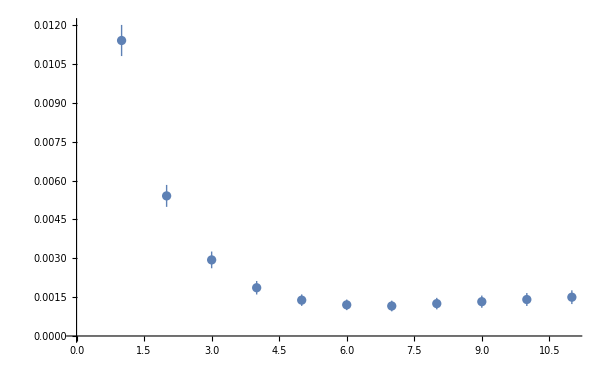

```mathematica
ListPlot[%110]
```

```mathematica
Table[%98[[x]][[3]],{x,100}]
```

{{{1,0.0111747},{2,0.00523285},{3,0.00280312},{4,0.00174642},{5,0.00128243},{6,0.00110587},{7,0.0010485},{8,0.00113607},{9,0.00120593},{10,0.00127579},{11,0.00135084}},{{1,0.0111518},{2,0.00520717},{3,0.00278799},{4,0.00172605},{5,0.00123433},{6,0.00103512},{7,0.000964631},{8,0.00103165},{9,0.00109408},{10,0.00116774},{11,0.00125525}},{{1,0.0119806},{2,0.00556238},{3,0.002891},{4,0.00171028},{5,0.00116081},{6,0.000936564},{7,0.000867218},{8,0.000893754},{9,0.000935639},{10,0.000981917},{11,0.00103007}},{{1,0.0109422},{2,0.00523012},{3,0.00288216},{4,0.00186702},{5,0.00142724},{6,0.00125769},{7,0.00121247},{8,0.0012821},{9,0.00136044},{10,0.00144543},{11,0.00153144}},{{1,0.0119264},{2,0.00561892},{3,0.00295766},{4,0.0017604},{5,0.00118354},{6,0.000932722},{7,0.000827067},{8,0.000839065},{9,0.00088699},{10,0.000947738},{11,0.00101203}},{{1,0.012202},{2,0.00581475},{3,0.00312212},{4,0.00191263},{5,0.0013514},{6,0.00111682},{7,0.00103719},{8,0.00112742},{9,0.0011859},{10,0.00125228},{11,0.00132976}},{{1,0.0115089},{2,0.00551864},{3,0.00304732},{4,0.00197465},{5,0.00145062},{6,0.0012551},{7,0.00115956},{8,0.00122673},{9,0.00128015},{10,0.00134793},{11,0.00143165}},{{1,0.0117615},{2,0.00558027},{3,0.00301752},{4,0.00187691},{5,0.00134966},{6,0.00112755},{7,0.00103179},{8,0.00112932},{9,0.00119673},{10,0.00126159},{11,0.00134114}},{{1,0.0122595},{2,0.00615957},{3,0.003551},{4,0.00233663},{5,0.00175255},{6,0.00151586},{7,0.00145456},{8,0.00149093},{9,0.00154742},{10,0.00161701},{11,0.00168873}},{{1,0.0103582},{2,0.00471039},{3,0.00246101},{4,0.00154711},{5,0.001183},{6,0.00109921},{7,0.00117283},{8,0.00139585},{9,0.00151468},{10,0.0016396},{11,0.00176151}},{{1,0.0123405},{2,0.00630635},{3,0.00374825},{4,0.00256501},{5,0.00199039},{6,0.00171126},{7,0.00155939},{8,0.00157224},{9,0.00160863},{10,0.00167645},{11,0.00175238}},{{1,0.0118151},{2,0.00555138},{3,0.0029896},{4,0.00186905},{5,0.00137093},{6,0.00116312},{7,0.00109146},{8,0.00116671},{9,0.00123357},{10,0.00130888},{11,0.00139338}},{{1,0.0124399},{2,0.00620813},{3,0.00351433},{4,0.00226636},{5,0.00163584},{6,0.00133551},{7,0.00119851},{8,0.00120395},{9,0.00125634},{10,0.00132259},{11,0.0014059}},{{1,0.0125509},{2,0.00596881},{3,0.00318725},{4,0.00193566},{5,0.00134074},{6,0.00109064},{7,0.00095569},{8,0.000927715},{9,0.000948077},{10,0.000982541},{11,0.00103573}},{{1,0.0117133},{2,0.0056737},{3,0.00324282},{4,0.00220834},{5,0.00173821},{6,0.0015542},{7,0.00151188},{8,0.00161737},{9,0.00169373},{10,0.00178662},{11,0.0018923}},{{1,0.0115141},{2,0.00549816},{3,0.00302013},{4,0.00193049},{5,0.00144698},{6,0.00123713},{7,0.00115098},{8,0.0012231},{9,0.00128383},{10,0.00135659},{11,0.00143687}},{{1,0.0113506},{2,0.00526902},{3,0.00274303},{4,0.00165562},{5,0.00116217},{6,0.000995531},{7,0.000978881},{8,0.00103328},{9,0.00110318},{10,0.00118233},{11,0.00125614}},{{1,0.0116684},{2,0.00546436},{3,0.00286721},{4,0.00169703},{5,0.00113886},{6,0.000898832},{7,0.000822681},{8,0.000868208},{9,0.000925844},{10,0.000998825},{11,0.00108038}},{{1,0.0110026},{2,0.00488574},{3,0.0023759},{4,0.00130292},{5,0.000856756},{6,0.000713384},{7,0.000674733},{8,0.000774142},{9,0.00083699},{10,0.000925197},{11,0.00100786}},{{1,0.0122194},{2,0.00606482},{3,0.00347254},{4,0.0022645},{5,0.00166929},{6,0.00137068},{7,0.00123628},{8,0.00122333},{9,0.00126085},{10,0.00131968},{11,0.00138962}},{{1,0.0108361},{2,0.00514006},{3,0.00281244},{4,0.00179261},{5,0.00134686},{6,0.00116415},{7,0.00112588},{8,0.0012629},{9,0.00137313},{10,0.00149343},{11,0.00162073}},{{1,0.0110865},{2,0.00508088},{3,0.00267827},{4,0.00168054},{5,0.00125259},{6,0.00111474},{7,0.00111281},{8,0.00125803},{9,0.00133557},{10,0.0014149},{11,0.00150174}},{{1,0.0116725},{2,0.0055778},{3,0.00301805},{4,0.00188137},{5,0.00137602},{6,0.00115042},{7,0.00108809},{8,0.00119787},{9,0.00129764},{10,0.00140369},{11,0.001524}},{{1,0.0112787},{2,0.00519585},{3,0.0027297},{4,0.00165262},{5,0.0011688},{6,0.000987357},{7,0.000933653},{8,0.00103322},{9,0.00110143},{10,0.00118276},{11,0.00126655}},{{1,0.0114582},{2,0.00550791},{3,0.00304772},{4,0.00196271},{5,0.00148872},{6,0.00127576},{7,0.0012008},{8,0.00131447},{9,0.00139746},{10,0.00149039},{11,0.00159463}},{{1,0.0120978},{2,0.0057428},{3,0.00318279},{4,0.00207542},{5,0.00159055},{6,0.00140693},{7,0.00137321},{8,0.00145645},{9,0.00152021},{10,0.00158797},{11,0.00165774}},{{1,0.0113042},{2,0.00533592},{3,0.0028827},{4,0.00179123},{5,0.00129906},{6,0.00110319},{7,0.00106664},{8,0.00113238},{9,0.0011932},{10,0.0012667},{11,0.00133647}},{{1,0.0118251},{2,0.00550432},{3,0.00287761},{4,0.00170766},{5,0.00118397},{6,0.000979147},{7,0.000928528},{8,0.000985887},{9,0.00104682},{10,0.0011197},{11,0.00119385}},{{1,0.0114907},{2,0.00541375},{3,0.0028566},{4,0.00175853},{5,0.0012802},{6,0.00110751},{7,0.00109446},{8,0.00120502},{9,0.00129172},{10,0.00138426},{11,0.0014784}},{{1,0.0109271},{2,0.00501917},{3,0.0026539},{4,0.0016592},{5,0.00123816},{6,0.00110986},{7,0.00110164},{8,0.00119264},{9,0.00127177},{10,0.00134143},{11,0.00141689}},{{1,0.0109695},{2,0.0054238},{3,0.00317133},{4,0.00221379},{5,0.00177102},{6,0.00159297},{7,0.00151595},{8,0.00162609},{9,0.00171746},{10,0.00182279},{11,0.00195506}},{{1,0.0121341},{2,0.00604861},{3,0.00346813},{4,0.00228885},{5,0.0016818},{6,0.00140992},{7,0.00127636},{8,0.00131748},{9,0.00137471},{10,0.00143989},{11,0.00152222}},{{1,0.0113346},{2,0.00522445},{3,0.00270587},{4,0.00162932},{5,0.00119266},{6,0.00106413},{7,0.0010851},{8,0.00118912},{9,0.00128207},{10,0.00137171},{11,0.00145982}},{{1,0.0122959},{2,0.00614908},{3,0.00351679},{4,0.00229254},{5,0.00167589},{6,0.00146813},{7,0.00145723},{8,0.00154637},{9,0.0016294},{10,0.00173083},{11,0.00182277}},{{1,0.0111882},{2,0.00528973},{3,0.00289696},{4,0.00188631},{5,0.00142672},{6,0.00126879},{7,0.00122932},{8,0.00131434},{9,0.00139272},{10,0.00148306},{11,0.00158655}},{{1,0.0112644},{2,0.00526157},{3,0.00279614},{4,0.00173122},{5,0.00125229},{6,0.00106059},{7,0.000987563},{8,0.00108645},{9,0.00115286},{10,0.00122516},{11,0.00130288}},{{1,0.0119423},{2,0.00594765},{3,0.00344489},{4,0.00233311},{5,0.00180841},{6,0.00164131},{7,0.00163655},{8,0.0018078},{9,0.00191123},{10,0.00203864},{11,0.00216575}},{{1,0.00999498},{2,0.00443448},{3,0.00225797},{4,0.00138372},{5,0.00104647},{6,0.000974974},{7,0.00101457},{8,0.00119317},{9,0.00131198},{10,0.00143269},{11,0.00155471}},{{1,0.0124623},{2,0.00613414},{3,0.00343976},{4,0.00223426},{5,0.00163328},{6,0.00137333},{7,0.0012254},{8,0.00124262},{9,0.00128527},{10,0.00134785},{11,0.00143311}},{{1,0.0118492},{2,0.00573163},{3,0.00319406},{4,0.00207369},{5,0.00153499},{6,0.00132253},{7,0.00121532},{8,0.00125166},{9,0.00129517},{10,0.00133909},{11,0.00140794}},{{1,0.0110309},{2,0.00527821},{3,0.00295433},{4,0.00202936},{5,0.00169746},{6,0.0016053},{7,0.00162655},{8,0.00175367},{9,0.00184089},{10,0.00193736},{11,0.00202547}},{{1,0.0112782},{2,0.00539973},{3,0.00298204},{4,0.00191892},{5,0.00143769},{6,0.00122772},{7,0.00113215},{8,0.00121866},{9,0.00127525},{10,0.00136148},{11,0.00145104}},{{1,0.0117436},{2,0.00564362},{3,0.00308984},{4,0.00195631},{5,0.00149449},{6,0.00131836},{7,0.00127178},{8,0.00139675},{9,0.00148635},{10,0.00158378},{11,0.00168412}},{{1,0.0105158},{2,0.00490005},{3,0.0026794},{4,0.00177543},{5,0.00141082},{6,0.00129583},{7,0.00131182},{8,0.00145037},{9,0.00155038},{10,0.00163827},{11,0.00172917}},{{1,0.0104002},{2,0.00468483},{3,0.00240969},{4,0.00150128},{5,0.00116299},{6,0.00106463},{7,0.00107624},{8,0.001204},{9,0.00128623},{10,0.00138496},{11,0.00147782}},{{1,0.0109239},{2,0.00500124},{3,0.00260271},{4,0.00159978},{5,0.00121904},{6,0.00113291},{7,0.00119136},{8,0.00138243},{9,0.00150032},{10,0.00162759},{11,0.00174829}},{{1,0.0115969},{2,0.00549956},{3,0.00298698},{4,0.00190324},{5,0.00142265},{6,0.00125336},{7,0.00119622},{8,0.00128039},{9,0.00135384},{10,0.00143156},{11,0.00152109}},{{1,0.0113088},{2,0.00518734},{3,0.00271588},{4,0.00168012},{5,0.00124256},{6,0.00110739},{7,0.00108467},{8,0.00118349},{9,0.00125311},{10,0.00132597},{11,0.00139346}},{{1,0.0111631},{2,0.00524941},{3,0.00281123},{4,0.00174565},{5,0.00128941},{6,0.0011275},{7,0.00110684},{8,0.00121182},{9,0.001309},{10,0.00140338},{11,0.00150145}},{{1,0.0113039},{2,0.00554402},{3,0.00319086},{4,0.0021519},{5,0.0016535},{6,0.00146506},{7,0.00141994},{8,0.00147898},{9,0.00154692},{10,0.0016207},{11,0.00171168}},{{1,0.0110417},{2,0.00516215},{3,0.00274833},{4,0.00174156},{5,0.00130915},{6,0.00117097},{7,0.00117174},{8,0.00132158},{9,0.00141645},{10,0.00151105},{11,0.00160846}},{{1,0.0111118},{2,0.00502359},{3,0.00254662},{4,0.00148245},{5,0.00104581},{6,0.000902061},{7,0.000904798},{8,0.00101196},{9,0.00108289},{10,0.00116041},{11,0.00122832}},{{1,0.0114902},{2,0.00537522},{3,0.00287345},{4,0.00180332},{5,0.00134258},{6,0.00117835},{7,0.00114334},{8,0.00120639},{9,0.00127176},{10,0.00132376},{11,0.00137944}},{{1,0.0120912},{2,0.00602051},{3,0.00347758},{4,0.00232568},{5,0.00183253},{6,0.00165943},{7,0.00166246},{8,0.00175248},{9,0.00182704},{10,0.00191059},{11,0.00198248}},{{1,0.0116145},{2,0.00551624},{3,0.00300074},{4,0.00191351},{5,0.00146911},{6,0.00130302},{7,0.00125496},{8,0.00137635},{9,0.00146309},{10,0.00157125},{11,0.0016856}},{{1,0.0116438},{2,0.00531982},{3,0.00272976},{4,0.00160859},{5,0.00112346},{6,0.000971857},{7,0.00095407},{8,0.00102736},{9,0.00110569},{10,0.00119228},{11,0.00127613}},{{1,0.0106526},{2,0.00491776},{3,0.00261951},{4,0.00165246},{5,0.00125539},{6,0.00112576},{7,0.00112406},{8,0.00117883},{9,0.00123731},{10,0.00130137},{11,0.00136255}},{{1,0.0108792},{2,0.00519506},{3,0.00286239},{4,0.00188087},{5,0.00147275},{6,0.0013517},{7,0.00139046},{8,0.00158355},{9,0.00170572},{10,0.00182305},{11,0.00194131}},{{1,0.0106239},{2,0.00478231},{3,0.00244385},{4,0.00147235},{5,0.001075},{6,0.000959956},{7,0.000964483},{8,0.00113501},{9,0.00123997},{10,0.00136076},{11,0.00147103}},{{1,0.0098017},{2,0.00466508},{3,0.00267769},{4,0.00190377},{5,0.00160884},{6,0.00156038},{7,0.00163392},{8,0.00184414},{9,0.00199569},{10,0.0021491},{11,0.00231505}},{{1,0.0116413},{2,0.00545566},{3,0.0028962},{4,0.00179164},{5,0.00131218},{6,0.00111575},{7,0.0010492},{8,0.00108388},{9,0.00113377},{10,0.00118566},{11,0.00124241}},{{1,0.0111933},{2,0.00528803},{3,0.00282887},{4,0.00174849},{5,0.00125974},{6,0.00104634},{7,0.000981851},{8,0.00107231},{9,0.00114219},{10,0.00122527},{11,0.00132707}},{{1,0.0117086},{2,0.00566875},{3,0.00316822},{4,0.00207867},{5,0.00158022},{6,0.00138883},{7,0.00132},{8,0.00140404},{9,0.00147043},{10,0.00155772},{11,0.00166044}},{{1,0.0106431},{2,0.00472441},{3,0.00237498},{4,0.00142827},{5,0.00107427},{6,0.000983155},{7,0.00101009},{8,0.00118371},{9,0.00128278},{10,0.00138208},{11,0.00148184}},{{1,0.0112277},{2,0.005456},{3,0.00305384},{4,0.00200296},{5,0.00148844},{6,0.00126653},{7,0.00116757},{8,0.0012297},{9,0.00129813},{10,0.00136814},{11,0.00146516}},{{1,0.0112568},{2,0.00537146},{3,0.00294501},{4,0.00186373},{5,0.00136395},{6,0.00117354},{7,0.00113535},{8,0.00119915},{9,0.00126675},{10,0.00133765},{11,0.00141077}},{{1,0.0110382},{2,0.00531635},{3,0.00296118},{4,0.0019206},{5,0.00146101},{6,0.00130828},{7,0.00130984},{8,0.00139276},{9,0.00148825},{10,0.00158079},{11,0.00166707}},{{1,0.011479},{2,0.00558141},{3,0.00309699},{4,0.00201172},{5,0.00151799},{6,0.00133782},{7,0.00132293},{8,0.00138831},{9,0.00146805},{10,0.00156434},{11,0.00165874}},{{1,0.0121252},{2,0.0060364},{3,0.00344072},{4,0.00223273},{5,0.00164682},{6,0.00138358},{7,0.00127126},{8,0.00132166},{9,0.00137221},{10,0.00143206},{11,0.00151131}},{{1,0.010952},{2,0.00507788},{3,0.00268184},{4,0.00163214},{5,0.00116735},{6,0.000990011},{7,0.000933323},{8,0.00103818},{9,0.00111221},{10,0.00118524},{11,0.00126972}},{{1,0.0111976},{2,0.00515414},{3,0.00271519},{4,0.00169375},{5,0.00126237},{6,0.00111465},{7,0.00110557},{8,0.00122823},{9,0.00130399},{10,0.00138869},{11,0.00146536}},{{1,0.0106413},{2,0.00470007},{3,0.00234858},{4,0.00137957},{5,0.00100832},{6,0.000923124},{7,0.000963001},{8,0.00113291},{9,0.00122901},{10,0.00132723},{11,0.00141496}},{{1,0.0114609},{2,0.00538079},{3,0.00288418},{4,0.00180111},{5,0.00131719},{6,0.00111091},{7,0.0010443},{8,0.00114269},{9,0.0012187},{10,0.00129867},{11,0.00138946}},{{1,0.0112772},{2,0.0052566},{3,0.00275892},{4,0.00168634},{5,0.00121147},{6,0.00103981},{7,0.00100821},{8,0.001109},{9,0.00117318},{10,0.00126051},{11,0.00133783}},{{1,0.0105862},{2,0.00478494},{3,0.00245527},{4,0.00148441},{5,0.00105945},{6,0.000914508},{7,0.000892191},{8,0.00100694},{9,0.00109642},{10,0.00119707},{11,0.00131069}},{{1,0.0108757},{2,0.00510167},{3,0.00273157},{4,0.00170557},{5,0.00125533},{6,0.00109937},{7,0.00104596},{8,0.00115372},{9,0.00124865},{10,0.00135355},{11,0.00146098}},{{1,0.0110876},{2,0.00506054},{3,0.00264579},{4,0.00163785},{5,0.00119803},{6,0.00104166},{7,0.00101142},{8,0.00113304},{9,0.0012005},{10,0.00126489},{11,0.00133776}},{{1,0.0109766},{2,0.00517745},{3,0.00280833},{4,0.00180763},{5,0.00140036},{6,0.00125708},{7,0.00122039},{8,0.0013706},{9,0.00146523},{10,0.00157616},{11,0.00169115}},{{1,0.0113486},{2,0.00551308},{3,0.00306676},{4,0.00196503},{5,0.00144047},{6,0.00122535},{7,0.00114576},{8,0.00117657},{9,0.00123619},{10,0.00131467},{11,0.00139983}},{{1,0.0124545},{2,0.00616566},{3,0.0035048},{4,0.00231171},{5,0.00175782},{6,0.00151822},{7,0.00143206},{8,0.00150812},{9,0.00158312},{10,0.00166652},{11,0.00176313}},{{1,0.0102631},{2,0.00491757},{3,0.00283156},{4,0.00202235},{5,0.00171466},{6,0.00169651},{7,0.00181481},{8,0.00203586},{9,0.0021789},{10,0.00231299},{11,0.00243954}},{{1,0.0107169},{2,0.00487999},{3,0.00251045},{4,0.00152633},{5,0.0011251},{6,0.00103573},{7,0.00109995},{8,0.00127341},{9,0.00139062},{10,0.00151345},{11,0.00163188}},{{1,0.0104158},{2,0.00462935},{3,0.00235813},{4,0.00145178},{5,0.00110686},{6,0.00102104},{7,0.00103815},{8,0.00119697},{9,0.00128399},{10,0.00137783},{11,0.00147093}},{{1,0.0123044},{2,0.00605167},{3,0.00337835},{4,0.00215265},{5,0.00154675},{6,0.00126619},{7,0.00113791},{8,0.00117985},{9,0.00122698},{10,0.00130405},{11,0.00140013}},{{1,0.0117302},{2,0.00587799},{3,0.00339193},{4,0.00228926},{5,0.00177658},{6,0.00155347},{7,0.00151293},{8,0.00162756},{9,0.00173253},{10,0.00185043},{11,0.00198093}},{{1,0.0115134},{2,0.00547443},{3,0.00298349},{4,0.00187971},{5,0.00138736},{6,0.00116607},{7,0.00108433},{8,0.00115624},{9,0.00121568},{10,0.00129276},{11,0.00137406}},{{1,0.0123902},{2,0.00625732},{3,0.00359554},{4,0.00236375},{5,0.0017449},{6,0.00143065},{7,0.00127115},{8,0.00132802},{9,0.00138973},{10,0.00147929},{11,0.00158372}},{{1,0.0117033},{2,0.00539474},{3,0.00278525},{4,0.00163779},{5,0.00110881},{6,0.000890084},{7,0.00079692},{8,0.000847843},{9,0.000884579},{10,0.00094177},{11,0.00100798}},{{1,0.0111627},{2,0.00508955},{3,0.00264326},{4,0.0016146},{5,0.00115109},{6,0.000993133},{7,0.000953422},{8,0.00105317},{9,0.00111703},{10,0.00119603},{11,0.00127916}},{{1,0.0116278},{2,0.00543237},{3,0.00284931},{4,0.00172417},{5,0.00122767},{6,0.001039},{7,0.00100659},{8,0.00106215},{9,0.00111911},{10,0.001174},{11,0.00122838}},{{1,0.011737},{2,0.00548673},{3,0.00290178},{4,0.00176545},{5,0.00124829},{6,0.00103964},{7,0.000970961},{8,0.0010112},{9,0.00105679},{10,0.00111156},{11,0.00117018}},{{1,0.010994},{2,0.00508913},{3,0.00267065},{4,0.00164767},{5,0.00121295},{6,0.00108081},{7,0.00106642},{8,0.00118137},{9,0.00126755},{10,0.00136033},{11,0.00145735}},{{1,0.0122097},{2,0.00594501},{3,0.0032664},{4,0.00203311},{5,0.0014277},{6,0.00115378},{7,0.00104045},{8,0.00107741},{9,0.00111948},{10,0.00117927},{11,0.00124584}},{{1,0.0123795},{2,0.00618913},{3,0.00352655},{4,0.00231181},{5,0.00169404},{6,0.00141427},{7,0.0012712},{8,0.0013106},{9,0.00135978},{10,0.00142745},{11,0.00151323}},{{1,0.0121531},{2,0.00585787},{3,0.00319772},{4,0.00198899},{5,0.00142339},{6,0.0011695},{7,0.00106297},{8,0.00112034},{9,0.00118485},{10,0.00125682},{11,0.00134204}},{{1,0.0109443},{2,0.00524913},{3,0.00292386},{4,0.00192586},{5,0.00147302},{6,0.00132346},{7,0.00131239},{8,0.00148042},{9,0.00158983},{10,0.00172428},{11,0.00186124}},{{1,0.0117282},{2,0.00549539},{3,0.00293238},{4,0.00181143},{5,0.00135938},{6,0.00118964},{7,0.0011136},{8,0.00114843},{9,0.00118128},{10,0.0012312},{11,0.00128165}},{{1,0.0123151},{2,0.00595344},{3,0.00330114},{4,0.00210779},{5,0.00154429},{6,0.00131238},{7,0.00122165},{8,0.00124227},{9,0.00127938},{10,0.00133122},{11,0.00138314}},{{1,0.0104829},{2,0.00489216},{3,0.00270012},{4,0.00178715},{5,0.00141138},{6,0.00128876},{7,0.0012783},{8,0.00142936},{9,0.00154406},{10,0.00166195},{11,0.00177802}},{{1,0.011542},{2,0.00547431},{3,0.00295395},{4,0.0018561},{5,0.00135175},{6,0.00116609},{7,0.0011257},{8,0.00120936},{9,0.00127754},{10,0.00134737},{11,0.00143042}}}

```mathematica
Table[%98[[3]]]
```

```mathematica
Table[%69[[x]][[2]],{x,10000}]
```

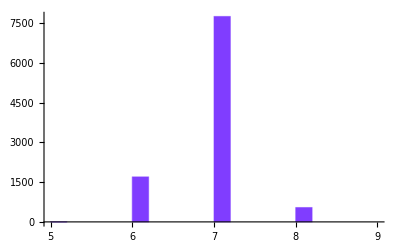

```mathematica
Histogram[%72,{5,9,0.2},ChartStyle->RGBColor[0.5,0.24,1]]
```

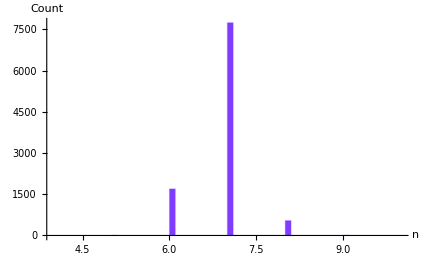

```mathematica
Show[%91,AxesLabel->{HoldForm[n],HoldForm[Count]},PlotLabel->None,LabelStyle->{16,GrayLevel[0]},ImageSize->{500,500}]
```

```mathematica
Table[%69[[x]][[3]],{x,10000}]
```

{{{1,0.0104373},{2,0.00483031},{3,0.00257808},{4,0.00162421},{5,0.00122958},{6,0.00110543},{7,0.00110714},{8,0.00126989},{9,0.00136456},{10,0.00147573}},9998,{{1,0.010925},{2,0.00515307},{3,0.00287816},{4,0.00190553},{5,0.00148527},{6,0.00134043},{7,0.00129847},{8,0.00137861},{9,0.00142978},{10,0.00147274}}}
 |  |  |  |

```mathematica
Table[%74[[1]][[x,2]],{x,10}]
```

{{1,0.0104373},{2,0.00483031},{3,0.00257808},{4,0.00162421},{5,0.00122958},{6,0.00110543},{7,0.00110714},{8,0.00126989},{9,0.00136456},{10,0.00147573}}

```mathematica
Table[Table[%74[[y]][[x,2]],{x,10}],{y,10000}]
```

{{0.0104373,0.00483031,0.00257808,0.00162421,0.00122958,0.00110543,0.00110714,0.00126989,0.00136456,0.00147573},{0.0115822,0.00563917,0.00312945,0.00202635,0.00152363,0.001289,0.00119969,0.00128957,0.00137718,0.00148738},9997,{0.010925,0.00515307,0.00287816,0.00190553,0.00148527,0.00134043,0.00129847,0.00137861,0.00142978,0.00147274}}
 |  |  |  |

```mathematica
ListPlot[Table[Around[Table[%80[[x]][[y]],{x,10000}]],{y,10}],PlotStyle->Directive[Blue,PointSize[0.015],"LineOpacity"->1]]
```

-Graphics-

```mathematica
Show[%118,AxesLabel->{HoldForm[n],HoldForm[χ]},(*PlotLabel->HoldForm[Misfit function],*)LabelStyle->{16,GrayLevel[0]},ImageSize->{500,500},PlotStyle->Directive[Blue,PointSize[0.02],"LineOpacity"->1]]
```

-Graphics-

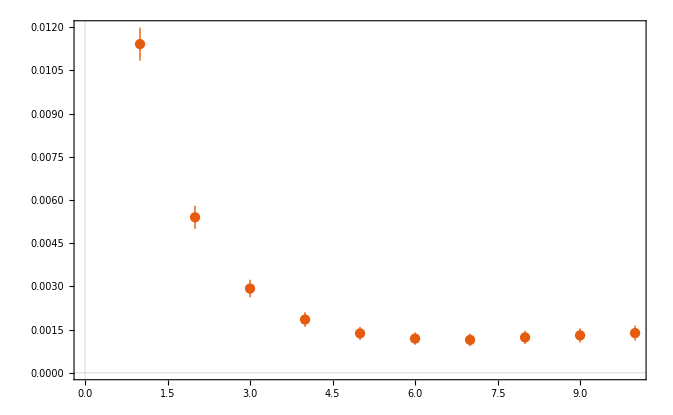

```mathematica
ListPlot[Table[Around[Table[%80⟦x⟧⟦y⟧,{x,10000}]],{y,10}],PlotTheme->"Scientific"]
```

```mathematica
ListPlot[Table[Around[Table[%80[[x]][[y]],{x,0000,10000}]],{y,10}]]
```

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

Part::partd: Part specification List⟦2⟧ is longer than depth of object.

Part::partd: Part specification List⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-